# Setup

```mathematica
(* ================================================================ *)
(* MODULE 0: SETUP                                                  *)
(* ================================================================ *)

baseDir = NotebookDirectory[];
Get[FileNameJoin[{baseDir, "QKT_full.wl"}]];
LaunchKernels[14];
```

# Helpers

```mathematica
(* ================================================================*)(*MODULE 2:HELPER PLOT FUNCTIONS*)(* ================================================================*)(*---Plot style---*)
$pOpts=Sequence[ImageSize->1000,Frame->True,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black]];
$legStyle=Directive[Black,18];

(*---Export helper---*)
SavePlot[plt_,name_]:=(Print[Style[name,14,Bold]];(*Adds a nice title above the plot*)Print[plt];                   (*Renders the plot directly in the notebook*));

(*---KL divergence---*)
KLDivergenceFromData[dataVals_List,theoryFunc_,binMin_:0,binMax_:4,binWidth_:0.05]:=Module[{edges,centers,hData,pD,pT,mask,dx},dx=binWidth;
edges=Range[binMin,binMax,dx];
centers=(Most[edges]+Rest[edges])/2;
hData=BinCounts[dataVals,{binMin,binMax,dx}]/Length[dataVals]/dx;
pD=hData*dx;
pT=Map[theoryFunc,centers]*dx;
mask=Flatten[Position[Thread[pD>0&&pT>0],True]];
If[Length[mask]==0,0.,Total[(pD[[mask]])*Log[pD[[mask]]/pT[[mask]]]]]];

(*---Staircase+residuals---*)
PlotStaircase[specData_,label_]:=Module[{vd=ValidateUnfolding[specData]},{Show[ListLinePlot[Transpose[{vd["Phases"],vd["EmpiricalCDF"]}],PlotStyle->{Blue,Thick}],Plot[x/(2 Pi),{x,0,2 Pi},PlotStyle->{Black,Dashed,Thick}],$pOpts,FrameLabel->{"θ","𝒩(θ)/N"},PlotLabel->label<>": Staircase",PlotRange->All],Show[ListLinePlot[Transpose[{vd["Phases"],vd["Residuals"]}],PlotStyle->{Blue,AbsoluteThickness[1]}],$pOpts,FrameLabel->{"θ","Residual (mean spacings)"},PlotLabel->label<>": Residuals",GridLines->{None,{0}},GridLinesStyle->Directive[Red,Dashed],PlotRange->All],vd["KS"]}];

(*---NNSD histogram---*)
PlotNNSD[spacings_,label_]:=Legended[Show[Histogram[spacings,{0,4,0.25},"ProbabilityDensity",ChartStyle->Directive[LightBlue,EdgeForm[Gray]],PlotRange->{{0,3.5},{0,1.1}}],Plot[WignerCOE[s],{s,0,3.5},PlotStyle->{Red,Thick}],Plot[Exp[-s],{s,0,3.5},PlotStyle->{Black,Dashed}],$pOpts,FrameLabel->{"s","P(s)"},PlotLabel->label<>": P(s)"],Placed[LineLegend[{Directive[Red,Thick],Directive[Black,Dashed]},{"COE surmise","Poisson"},LabelStyle->$legStyle],{Right,Top}]];

(*---Cumulative I(s) with KS+DKL---*)
PlotCumulativeS[spacings_,label_]:=Module[{sorted,nSp,empCDF,coeCDF,ks,dkl},sorted=Sort[spacings];nSp=Length[sorted];
empCDF=Range[nSp]/nSp;
coeCDF=IntWignerCOE/@sorted;
ks=Max[Abs[empCDF-coeCDF]];
dkl=KLDivergenceFromData[spacings,WignerCOE,0,4,0.05];
Legended[Show[ListLinePlot[Transpose[{sorted,empCDF}],PlotStyle->{Blue,Thick},PlotRange->{{0,3.5},{0,1}}],Plot[IntWignerCOE[s],{s,0,3.5},PlotStyle->{Red,Thick}],Plot[1-Exp[-s],{s,0,3.5},PlotStyle->{Black,Dashed}],$pOpts,FrameLabel->{"s","I(s)"},PlotLabel->label<>": I(s)  |  KS = "<>ToString[NumberForm[ks,4]]],Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick],Directive[Black,Dashed]},{"Data","COE","Poisson"},LabelStyle->$legStyle],{Right,Bottom}]]];

(*---P(r) histogram---*)
PlotPrHist[ratios_,label_]:=Legended[Show[Histogram[ratios,{0,1,0.25},"ProbabilityDensity",ChartStyle->Directive[LightBlue,EdgeForm[Gray]],PlotRange->{{0,1},{0,2.2}}],Plot[PrCOE[r],{r,0,1},PlotStyle->{Red,Thick}],Plot[PrCUE[r],{r,0,1},PlotStyle->{Blue,Thick,Dashed}],Plot[PrPoisson[r],{r,0,1},PlotStyle->{Black,Dashed}],$pOpts,FrameLabel->{"r","P(r)"},PlotLabel->label<>": P(r)"],Placed[LineLegend[{Directive[Red,Thick],Directive[Blue,Thick,Dashed],Directive[Black,Dashed]},{"COE (β=1)","CUE (β=2)","Poisson"},LabelStyle->$legStyle],{Right,Top}]];

(*---Cumulative I(r) with KS+DKL---*)
PlotCumulativeR[ratios_,label_]:=Module[{sorted,nR,step,idx,sR,eC,cC,ks,dkl},sorted=Sort[ratios];nR=Length[sorted];
step=Max[1,Floor[nR/1000]];
idx=Range[1,nR,step];
sR=sorted[[idx]];
eC=Range[Length[idx]]/Length[idx];
cC=IntPrCOE/@sR;
ks=Max[Abs[eC-cC]];
dkl=KLDivergenceFromData[ratios,PrCOE,0,1,0.02];
Legended[Show[ListLinePlot[Transpose[{sR,eC}],PlotStyle->{Blue,Thick},PlotRange->{{0,1},{0,1}}],ListLinePlot[Transpose[{sR,cC}],PlotStyle->{Red,Thick}],$pOpts,FrameLabel->{"r","I(r)"},PlotLabel->label<>": I(r)  |  KS="<>ToString[NumberForm[ks,4]]],Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick]},{"Data","COE"},LabelStyle->$legStyle],{Right,Bottom}]]];

(*---Sigma2 comparison---*)
PlotSigma2[s2Even_,s2Odd_,s2COE_,label_]:=Legended[Show[ListLinePlot[{Transpose[{s2COE["LValues"],s2COE["Sigma2TheorMean"]+s2COE["SETheorMean"]}],Transpose[{s2COE["LValues"],s2COE["Sigma2TheorMean"]-s2COE["SETheorMean"]}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.15],Red]],ListLinePlot[Transpose[{s2COE["LValues"],s2COE["Sigma2TheorMean"]}],PlotStyle->{Red,Thick}],ListLinePlot[{Transpose[{s2Even["LValues"],s2Even["Sigma2TheorMean"]+s2Even["SETheorMean"]}],Transpose[{s2Even["LValues"],s2Even["Sigma2TheorMean"]-s2Even["SETheorMean"]}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.15],Blue]],ListLinePlot[Transpose[{s2Even["LValues"],s2Even["Sigma2TheorMean"]}],PlotStyle->{Blue,Thick}],ListLinePlot[{Transpose[{s2Odd["LValues"],s2Odd["Sigma2TheorMean"]+s2Odd["SETheorMean"]}],Transpose[{s2Odd["LValues"],s2Odd["Sigma2TheorMean"]-s2Odd["SETheorMean"]}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.15],Darker[Green]]],ListLinePlot[Transpose[{s2Odd["LValues"],s2Odd["Sigma2TheorMean"]}],PlotStyle->{Darker[Green],Thick}],Plot[COEAsymptoticSigma2[L],{L,0.5,Lmax},PlotStyle->{Orange,Thick,Dashed}],Plot[L,{L,0.5,Lmax},PlotStyle->{Black,Dashed,Thin}],$pOpts,FrameLabel->{"L","\!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->label,PlotRange->{All,{0,Automatic}}],Placed[LineLegend[{Directive[Blue,Thick],Directive[Darker[Green],Thick],Directive[Red,Thick],Directive[Orange,Thick,Dashed],Directive[Black,Dashed,Thin]},{"Even","Odd","COE("<>ToString[nCOE]<>")","COE asymptotic","Poisson"},LabelStyle->$legStyle],{Right,Bottom}]];

(*---Residual---*)
PlotResidual[s2Even_,s2Odd_,s2COE_,label_]:=Module[{nMin,lR,resE,resO,seE,seO},nMin=Min[Length[s2Even["LValues"]],Length[s2Odd["LValues"]],Length[s2COE["LValues"]]];
lR=s2COE["LValues"][[1;;nMin]];
resE=s2Even["Sigma2TheorMean"][[1;;nMin]]-s2COE["Sigma2TheorMean"][[1;;nMin]];
resO=s2Odd["Sigma2TheorMean"][[1;;nMin]]-s2COE["Sigma2TheorMean"][[1;;nMin]];
seE=Sqrt[s2Even["SETheorMean"][[1;;nMin]]^2+s2COE["SETheorMean"][[1;;nMin]]^2];
seO=Sqrt[s2Odd["SETheorMean"][[1;;nMin]]^2+s2COE["SETheorMean"][[1;;nMin]]^2];
Legended[Show[ListLinePlot[{Transpose[{lR,resE+seE}],Transpose[{lR,resE-seE}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.2],Blue]],ListLinePlot[Transpose[{lR,resE}],PlotStyle->{Blue,Thick}],ListLinePlot[{Transpose[{lR,resO+seO}],Transpose[{lR,resO-seO}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.2],Darker[Green]]],ListLinePlot[Transpose[{lR,resO}],PlotStyle->{Darker[Green],Thick}],Plot[0,{x,0,Max[lR]},PlotStyle->{Red,Dashed}],$pOpts,FrameLabel->{"L","\!\(\*SuperscriptBox[\(σ\), \(2\)]\)(QKT) - \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(COE)"},PlotLabel->label,PlotRange->All],Placed[LineLegend[{Directive[Blue,Thick],Directive[Darker[Green],Thick]},{"Even - COE","Odd - COE"},LabelStyle->$legStyle],{Right,Bottom}]]];

(*---Dual estimator---*)
PlotDualEstimator[s2_,label_]:=Module[{rd},rd=Abs[s2["Sigma2TheorMean"]-s2["Sigma2SampleMean"]]/(s2["Sigma2TheorMean"]+10^-10);
ListLinePlot[Transpose[{s2["LValues"],rd}],Filling->Axis,FillingStyle->Directive[Opacity[0.3],Blue],$pOpts,PlotRange->{0,All},FrameLabel->{"L","Relative difference"},PlotLabel->label<>": Dual Estimator"]];

(*---Fluctuating staircase---*)
PlotFluctuations[flucEven_,flucOdd_,label_]:=Legended[Show[ListLinePlot[Transpose[{flucEven["x"],flucEven["delta"]}],PlotStyle->{Blue,AbsoluteThickness[0.5]}],ListLinePlot[Transpose[{flucOdd["x"],flucOdd["delta"]}],PlotStyle->{Darker[Green],AbsoluteThickness[0.5]}],$pOpts,FrameLabel->{"Unfolded level index x","\!\(\*OverscriptBox[\(N\), \(~\)]\)(x)"},PlotLabel->label<>": Fluctuating Staircase",GridLines->{None,{0}},GridLinesStyle->Directive[Red,Dashed],PlotRange->All],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[1.5]],Directive[Darker[Green],AbsoluteThickness[1.5]]},{"Even","Odd"},LabelStyle->$legStyle],{Right,Bottom}]];

(*---Length spectrum---*)
PlotLengthSpectrum[lsEven_,lsOdd_,label_,nShow_:50]:=Legended[Show[ListLinePlot[Transpose[{lsEven["Period"][[1;;nShow]],lsEven["Amplitude"][[1;;nShow]]}],PlotStyle->{Blue,AbsoluteThickness[1.5]}],ListLinePlot[Transpose[{lsOdd["Period"][[1;;nShow]],lsOdd["Amplitude"][[1;;nShow]]}],PlotStyle->{Red,AbsoluteThickness[1.5]}],$pOpts,FrameLabel->{"Period (kicks)","Length Spectrum"},PlotLabel->label<>": Length Spectrum",GridLines->{None,{0}},GridLinesStyle->Directive[Gray,Dashed]],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[1.5]],Directive[Red,AbsoluteThickness[1.5]]},{"Even","Odd"},LabelStyle->$legStyle],{Right,Bottom}]];

(*---SFF---*)
PlotSFF[sffEvenEns_,sffOddEns_,sffCOE_,label_]:=Legended[Show[ListLinePlot[{Transpose[{sffCOE["Tau"],sffCOE["MeanK"]+sffCOE["SE"]}],Transpose[{sffCOE["Tau"],sffCOE["MeanK"]-sffCOE["SE"]}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.15],Red]],ListLinePlot[Transpose[{sffCOE["Tau"],sffCOE["MeanK"]}],PlotStyle->{Red,Thick}],ListLinePlot[{Transpose[{sffEvenEns["Tau"],sffEvenEns["MeanK"]+sffEvenEns["SE"]}],Transpose[{sffEvenEns["Tau"],sffEvenEns["MeanK"]-sffEvenEns["SE"]}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.15],Blue]],ListLinePlot[Transpose[{sffEvenEns["Tau"],sffEvenEns["MeanK"]}],PlotStyle->{Blue,Thick}],ListLinePlot[{Transpose[{sffOddEns["Tau"],sffOddEns["MeanK"]+sffOddEns["SE"]}],Transpose[{sffOddEns["Tau"],sffOddEns["MeanK"]-sffOddEns["SE"]}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.15],Darker[Green]]],ListLinePlot[Transpose[{sffOddEns["Tau"],sffOddEns["MeanK"]}],PlotStyle->{Darker[Green],Thick}],Plot[COESFFAnalytical[tau],{tau,0.001,tauMax},PlotStyle->{Black,Thick,Dashed}],$pOpts,FrameLabel->{"τ","K(τ)"},PlotLabel->label<>": SFF",PlotRange->{{0,tauMax},{0,1.5}}],Placed[LineLegend[{Directive[Blue,Thick],Directive[Darker[Green],Thick],Directive[Red,Thick],Directive[Black,Thick,Dashed]},{"Even","Odd","COE("<>ToString[nCOE]<>")","COE analytical"},LabelStyle->$legStyle],{Right,Bottom}]];

(*---IPR distribution---*)
(*PlotIPR[iprsEven_,iprsOdd_,nDim_,label_,max_]:=Legended[Show[Histogram[{iprsEven,iprsOdd},Automatic,"Probability",ChartStyle->{Directive[Blue,Opacity[0.5]],Directive[Darker[Green],Opacity[0.5]]}],Graphics[{Red,Dashed,AbsoluteThickness[2],Line[{{3.0/nDim,0},{3.0/nDim,Max[iprsEven]}}]}],$pOpts,FrameLabel->{"IPR","Density"},PlotLabel->label<>": IPR Distribution",PlotRange->{All,All}],Placed[LineLegend[{Directive[Blue,Opacity[0.5]],Directive[Darker[Green],Opacity[0.5]],Directive[Red,Dashed]},{"Even","Odd","COE: 3/N"},LabelStyle->$legStyle],{Right,Top}]];*)
PlotIPR[iprsEven_,iprsOdd_,nDim_,label_]:=Legended[Show[Histogram[{iprsEven,iprsOdd},Automatic,"Probability",ChartStyle->{Directive[Blue,Opacity[0.5]],Directive[Darker[Green],Opacity[0.5]]}],(*FIXED HERE:InfiniteLine replaces Line*)Graphics[{Red,Dashed,AbsoluteThickness[2],InfiniteLine[{3.0/nDim,0},{0,1}]}],$pOpts,FrameLabel->{"IPR","Density"},PlotLabel->label<>": IPR Distribution",PlotRange->{All,All}],Placed[LineLegend[{Directive[Blue,Opacity[0.5]],Directive[Darker[Green],Opacity[0.5]],Directive[Red,Dashed]},{"Even","Odd","COE: 3/N"},LabelStyle->$legStyle],{Right,Top}]]
```

```mathematica
(* ================================================================ *)
(* DEFINITIONS                                                      *)
(* ================================================================ *)

ClearAll[IntPrCOETable, IntPrCOEFast, GetFluctuationsCentered,
  ExtractSpacingsAndRatios, MakeRowPlots];

(* --- Build fast COE ratio CDF lookup (replaces $IntPrCOEInterp) --- *)
IntPrCOETable = Table[
  {r, NIntegrate[PrCOE[x], {x, 0, r}]}, {r, 0, 1, 0.001}];
IntPrCOEFast = Interpolation[IntPrCOETable];
Print["IntPrCOEFast test: ", IntPrCOEFast[0.5]];  (* should be ~0.458 *)

(* --- Fluctuations centered on zero --- *)
GetFluctuationsCentered[specData_Association] :=
  Module[{x = specData["Spectrum"], n = specData["N"], raw},
    raw = Range[n] - x;
    <|"x" -> x, "delta" -> raw - Mean[raw], "N" -> n|>
  ];

(* --- Extract spacings + ratios from one spectrum --- *)
ExtractSpacingsAndRatios[specData_Association] :=
  Module[{spacings, sp, ratios},
    spacings = NNSpacings[specData];
    sp = Differences[specData["Spectrum"]];
    ratios = Min /@ Transpose[{Most[sp] / Rest[sp], Rest[sp] / Most[sp]}];
    <|"Spacings" -> spacings, "SortedS" -> Sort[spacings],
      "Ratios" -> ratios, "SortedR" -> Sort[ratios]|>
  ];

(* --- Compact plot options --- *)
$cOpts = Sequence[Frame -> True,
  FrameStyle -> Directive[Black, 16],
  LabelStyle -> Directive[Black, 16]];
$cSize = 380;

(* --- All plots for one sector --- *)
MakeRowPlots[sortedS_List, sortedR_List, flucData_Association, label_String] :=
  Module[{nS, nR, empS, empR, theoS, theoR, ksS, ksR,
          diffS, diffR, pPDFS, pPDFR, pCDFS, pCDFR,
          pMSDS, pMSDR, pCDFRplot, pFluc},

    nS = Length[sortedS]; nR = Length[sortedR];
    empS  = N[Range[nS] / nS];
    empR  = N[Range[nR] / nR];
    theoS = N[IntWignerCOE /@ sortedS];
    theoR = N[IntPrCOEFast /@ sortedR];

    ksS = Max[Abs[empS - theoS]];
    ksR = Max[Abs[empR - theoR]];
    diffS = (empS - theoS)^2;
    diffR = (empR - theoR)^2;

    (* P(s) *)
    pPDFS = Show[
      Histogram[sortedS, {0, 4, 0.1}, "ProbabilityDensity",
        ChartStyle -> Directive[LightGray, EdgeForm[Gray]],
        PlotRange -> {{0, 3.5}, {0, 1.1}}],
      Plot[WignerCOE[x], {x, 0, 3.5}, PlotStyle -> {Red, Dashed, Thick}],
      Plot[Exp[-x], {x, 0, 3.5}, PlotStyle -> {Black, Dashed}],
      $cOpts, FrameLabel -> {"s", "P(s)"},
      PlotLabel -> label <> " P(s)", ImageSize -> $cSize];

(* I(s) *)
    pCDFS = Show[
      ListLinePlot[Transpose[{sortedS, empS}],
        PlotStyle -> {Blue, Thick}, PlotRange -> {{0, 3.5}, {0, 1}}],
      Plot[IntWignerCOE[x], {x, 0, 3.5}, PlotStyle -> {Red, Dashed}],
      Plot[1 - Exp[-x], {x, 0, 3.5}, PlotStyle -> {Black, Dashed}],
      $cOpts, FrameLabel -> {"s", "I(s)"},
      PlotLabel -> label <> " I(s)  KS = " <> ToString[NumberForm[ksS, 4]],
      ImageSize -> $cSize];

    (* CDF diff (s) *)
    pMSDS = ListLinePlot[Transpose[{sortedS, diffS}],
      PlotStyle -> {Blue, Thick}, Filling -> Axis,
      FillingStyle -> Directive[Opacity[0.3], Blue],
      $cOpts, FrameLabel -> {"s", "(I-I_COE)^2"},
      PlotLabel -> label <> " CDF diff (s)",
      PlotRange -> All, ImageSize -> $cSize];

    (* P(r) *)
    pPDFR = Show[
      Histogram[sortedR, {0, 1, 0.05}, "ProbabilityDensity",
        ChartStyle -> Directive[LightGray, EdgeForm[Gray]],
        PlotRange -> {{0, 1}, {0, 2.2}}],
      Plot[PrCOE[x], {x, 0, 1}, PlotStyle -> {Red, Dashed, Thick}],
      Plot[PrPoisson[x], {x, 0, 1}, PlotStyle -> {Black, Dashed}],
      $cOpts, FrameLabel -> {"r", "P(r)"},
      PlotLabel -> label <> " P(r)", ImageSize -> $cSize];

    (* I(r) *)
    pCDFRplot = Show[
      ListLinePlot[Transpose[{sortedR, empR}],
        PlotStyle -> {Blue, Thick}, PlotRange -> {{0, 1}, {0, 1}}],
      ListLinePlot[Transpose[{sortedR, theoR}],
        PlotStyle -> {Red, Dashed}],
      $cOpts, FrameLabel -> {"r", "I(r)"},
      PlotLabel -> label <> " I(r)  KS = " <> ToString[NumberForm[ksR, 4]],
      ImageSize -> $cSize];

    (* CDF diff (r) *)
    pMSDR = ListLinePlot[Transpose[{sortedR, diffR}],
      PlotStyle -> {Blue, Thick}, Filling -> Axis,
      FillingStyle -> Directive[Opacity[0.3], Blue],
      $cOpts, FrameLabel -> {"r", "(I-I_COE)^2"},
      PlotLabel -> label <> " CDF diff (r)",
      PlotRange -> All, ImageSize -> $cSize];

    (* Fluctuation *)
    pFluc = ListLinePlot[Transpose[{flucData["x"], flucData["delta"]}],
      PlotStyle -> {Blue, AbsoluteThickness[0.5]},
      $cOpts,
      FrameLabel -> {"x", "\!\(\*OverscriptBox[\(N\), \(~\)]\)(x)"},
      PlotLabel -> label <> " Fluctuation",
      GridLines -> {None, {0}},
      GridLinesStyle -> Directive[Red, Dashed],
      ImageSize -> $cSize];

    (* Return: P(s), P(r), I(s), I(r), diff(s), diff(r), fluc *)
    {pPDFS,pCDFS,pMSDS,pPDFR, pCDFRplot, pMSDR, pFluc}
  ];
```

IntPrCOEFast test: 0.460051

```mathematica
(* ================================================================ *)
(* DEFINITIONS                                                      *)
(* ================================================================ *)

ClearAll[IntPrCOETable, IntPrCOEFast,
  KSFromSorted, CvMFromSorted, MSDFromSorted,
  ComputeGoFSingle, ComputeGoFEnsemble];

(* --- Build fast COE ratio CDF interpolator --- *)
IntPrCOETable = Table[
  {r, NIntegrate[PrCOE[x], {x, 0, r}]}, {r, 0, 1, 0.001}];
IntPrCOEFast = Interpolation[IntPrCOETable];
Print["IntPrCOEFast[0.5] = ", IntPrCOEFast[0.5]];

(* --- KS statistic from sorted data and CDF values --- *)
KSFromSorted[empCDF_List, theoCDFvals_List] :=
  Max[Abs[empCDF - theoCDFvals]];

(* --- Cramér–von Mises from sorted data --- *)
(* W^2 = (1/12n) + sum_i [(2i-1)/(2n) - F(x_i)]^2 / n *)
CvMFromSorted[n_Integer, theoCDFvals_List] :=
  Module[{midEmp},
    midEmp = N[(2 Range[n] - 1) / (2 n)];
    Total[(midEmp - theoCDFvals)^2] / n + 1 / (12 n)
  ];

(* --- MSD: mean of (F_emp - F_theo)^2 over data points --- *)
MSDFromSorted[empCDF_List, theoCDFvals_List] :=
  Mean[(empCDF - theoCDFvals)^2];

(* --- Compute all GoF metrics for one spectrum (pure numerical) --- *)
(* Returns: {KS_s, CvM_s, MSD_s, KS_r, CvM_r, MSD_r} *)
ComputeGoFSingle[specData_Association] :=
  Module[{spacings, sp, ratios, sortS, sortR, nS, nR,
          empS, empR, theoS, theoR,
          ksS, cvmS, msdS, ksR, cvmR, msdR},
    (* Spacings *)
    spacings = NNSpacings[specData];
    sortS = Sort[spacings];
    nS = Length[sortS];
    empS = N[Range[nS] / nS];
    theoS = N[IntWignerCOE /@ sortS];

    (* Ratios *)
    sp = Differences[specData["Spectrum"]];
    ratios = Min /@ Transpose[{Most[sp] / Rest[sp], Rest[sp] / Most[sp]}];
    sortR = Sort[ratios];
    nR = Length[sortR];
    empR = N[Range[nR] / nR];
    theoR = N[IntPrCOEFast /@ sortR];

    (* Metrics *)
    ksS  = KSFromSorted[empS, theoS];
    cvmS = CvMFromSorted[nS, theoS];
    msdS = MSDFromSorted[empS, theoS];

    ksR  = KSFromSorted[empR, theoR];
    cvmR = CvMFromSorted[nR, theoR];
    msdR = MSDFromSorted[empR, theoR];

    {ksS, cvmS, msdS, ksR, cvmR, msdR}
  ];

(* --- Compute GoF for pooled ensemble --- *)
ComputeGoFEnsemble[spectraList_List] :=
  Module[{allSpacings, allRatios, sortS, sortR, nS, nR,
          empS, empR, theoS, theoR,
          ksS, cvmS, msdS, ksR, cvmR, msdR, sp},
    allSpacings = Sort[Flatten[Map[NNSpacings, spectraList]]];
    sp = Flatten[Map[
      Function[{specData},
        Module[{d = Differences[specData["Spectrum"]]},
          Min /@ Transpose[{Most[d] / Rest[d], Rest[d] / Most[d]}]
        ]
      ], spectraList]];
    allRatios = Sort[sp];

    sortS = allSpacings; nS = Length[sortS];
    sortR = allRatios;   nR = Length[sortR];

    empS = N[Range[nS] / nS];
    empR = N[Range[nR] / nR];
    theoS = N[IntWignerCOE /@ sortS];
    theoR = N[IntPrCOEFast /@ sortR];

    ksS  = KSFromSorted[empS, theoS];
    cvmS = CvMFromSorted[nS, theoS];
    msdS = MSDFromSorted[empS, theoS];

    ksR  = KSFromSorted[empR, theoR];
    cvmR = CvMFromSorted[nR, theoR];
    msdR = MSDFromSorted[empR, theoR];

    <|"KS_s" -> ksS, "CvM_s" -> cvmS, "MSD_s" -> msdS,
      "KS_r" -> ksR, "CvM_r" -> cvmR, "MSD_r" -> msdR,
      "N_spacings" -> nS, "N_ratios" -> nR|>
  ];
```

IntPrCOEFast[0.5] = 0.460051

# Parameters

```mathematica
(* ================================================================ *)
(* MODULE 1: GLOBAL PARAMETERS                                     *)
(* ================================================================ *)

J       = 500;
alpha   = 0.84;
kCenter = 27.5;
delta   = 0.001;
nQKT    = 500;
```

```mathematica
(* --- Directories --- *)
EnsureDir[dir_] := If[!DirectoryQ[dir],
  CreateDirectory[dir, CreateIntermediateDirectories -> True]];

runLabel = "J" <> ToString[J] <> "_k" <> ToString[N[kCenter]];
resultsDir = FileNameJoin[{baseDir, "Results", runLabel}];
evenDir    = FileNameJoin[{resultsDir, "Even"}];
oddDir     = FileNameJoin[{resultsDir, "Odd"}];
plotDir    = FileNameJoin[{resultsDir, "plots"}];
EnsureDir[evenDir]; EnsureDir[oddDir]; EnsureDir[plotDir];

(* --- Plot style --- *)
$pOpts = Sequence[ImageSize -> 800, Frame -> True,
  FrameStyle -> Directive[27, Black],
  LabelStyle -> Directive[27, Black]];
$legStyle = Directive[Black, 18];
```

# QKT

```mathematica
(* ================================================================ *)
(* MODULE 4: QKT ENSEMBLE                                          *)
(* ================================================================ *)

(*Instead of using RandomReal to generate a list,hardcode it as a single value list*)
kList=RandomReal[{kCenter-delta,kCenter+delta},nQKT];
Print["\nDiagonalizing single QKT matrix (J=",J,", k=",kCenter,")..."];
AbsoluteTiming[qktEnsemble=GenerateQKTEnsemble[J,alpha,kList];]
Print["Even N = ",qktEnsemble["Even"][[1]]["N"],", Odd N = ",qktEnsemble["Odd"][[1]]["N"]];

dimE = qktEnsemble["Even"][[1]]["N"];
dimO = qktEnsemble["Odd"][[1]]["N"];
Print["  Even N = ", dimE, ", Odd N = ", dimO];

(* --- Export spectra --- *)
Export[FileNameJoin[{evenDir, "spectra.wdx"}], qktEnsemble["Even"], "WDX"];
Export[FileNameJoin[{oddDir, "spectra.wdx"}], qktEnsemble["Odd"], "WDX"];
Print["  Spectra exported"];
```

Diagonalizing single QKT matrix (J=500, k=27.5)...

{29.5291,Null}

Even N = 501, Odd N = 500

Even N = 501, Odd N = 500

Spectra exported

=== UNFOLDING VALIDATION ===

--- Even ---

KS: mean=0.1205, max=0.1762

Even_staircase

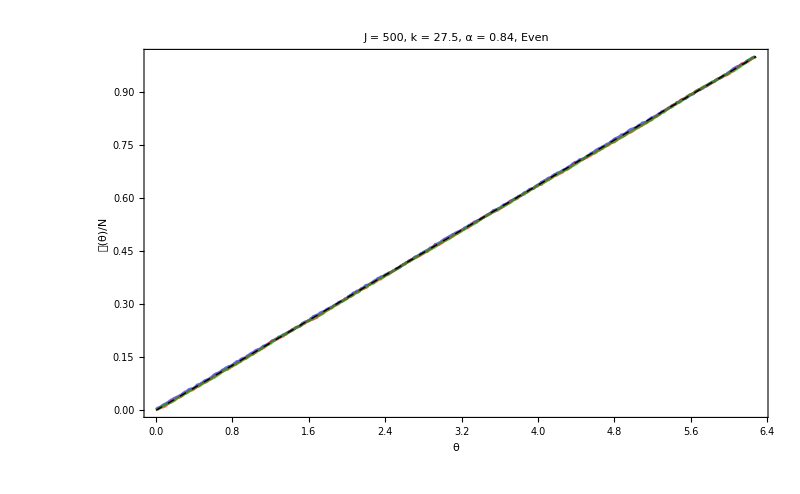

Even_residuals

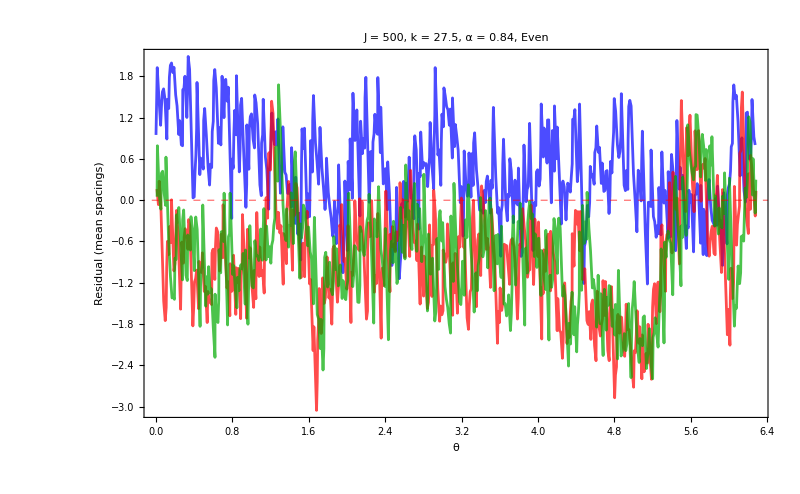

--- Odd ---

KS: mean=0.1161, max=0.1604

Odd_staircase

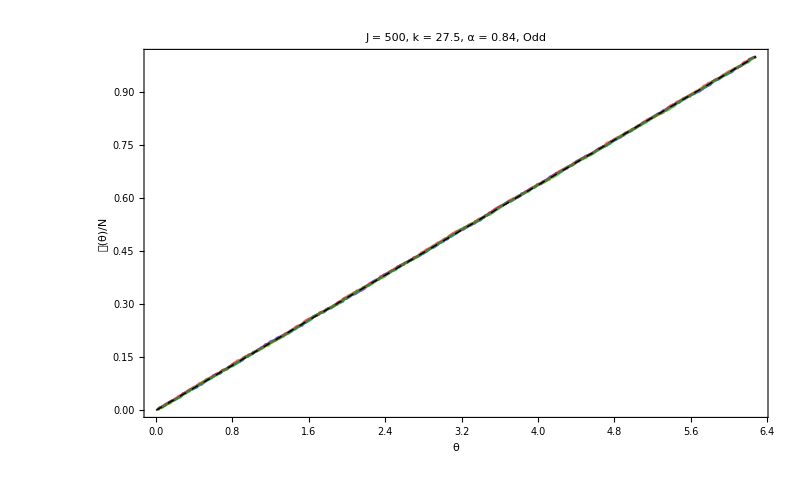

Odd_residuals

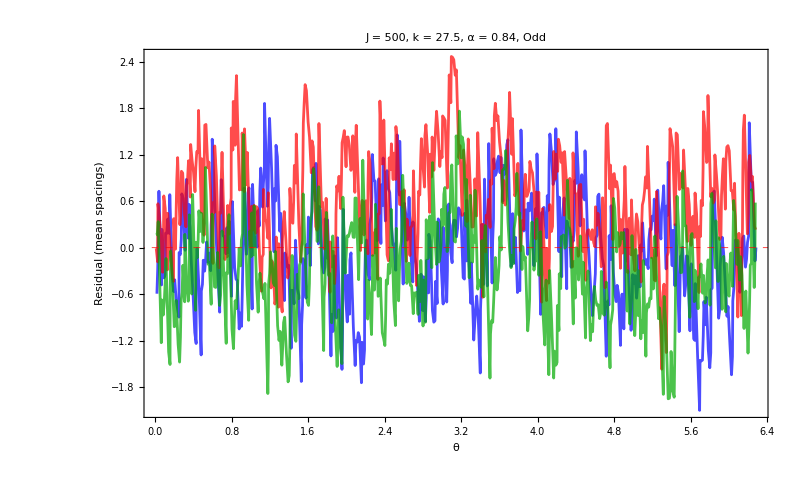

```mathematica
(* ================================================================ *)
(* MODULE 5: UNFOLDING VALIDATION                                   *)
(* ================================================================ *)

Print["\n=== UNFOLDING VALIDATION ==="];
Do[
  specList = qktEnsemble[sec];
  nR = Length[specList];
  sIdx = Round[Subdivide[1, nR, 2]];
  vd = Map[ValidateUnfolding, specList[[sIdx]]];
  allKS = Map[ValidateUnfolding[#]["KS"] &, specList];

  Print["--- ", sec, " ---"];
  Print["  KS: mean=", NumberForm[Mean[allKS], 4],
    ", max=", NumberForm[Max[allKS], 4]];

mainLabel = "J = " <>
  ToString[J] <> ", k = " <> ToString[N[kCenter]]<>", α = "<>ToString[alpha]<>", "<>sec;

  SavePlot[Show[
    Table[ListLinePlot[
      Transpose[{vd[[i]]["Phases"], vd[[i]]["EmpiricalCDF"]}],
      PlotStyle -> {{Blue, Red, Darker[Green]}[[i]], Opacity[0.6]}
    ], {i, 3}],
    Plot[x / (2 Pi), {x, 0, 2 Pi}, PlotStyle -> {Black, Dashed, Thick}],
    $pOpts, FrameLabel -> {"θ", "𝒩(θ)/N"},
    PlotLabel -> mainLabel,PlotRange->All
  ], sec <> "_staircase"];

  SavePlot[Show[
    Table[ListLinePlot[
      Transpose[{vd[[i]]["Phases"], vd[[i]]["Residuals"]}],
      PlotStyle -> {{Blue, Red, Darker[Green]}[[i]], Opacity[0.7]}
    ], {i, 3}],
    $pOpts, FrameLabel -> {"θ", "Residual (mean spacings)"},
    PlotLabel -> mainLabel,
    GridLines -> {None, {0}}, GridLinesStyle -> Directive[Red, Dashed],PlotRange->All
  ], sec <> "_residuals"];
, {sec, {"Even", "Odd"}}];
```

=== SPACING STATISTICS ===

--- Even ---

<s>=1., Var(s)=0.28859  (COE: 0.2732)

<r>=0.52854  (COE: 0.5359)

Even_nnsd

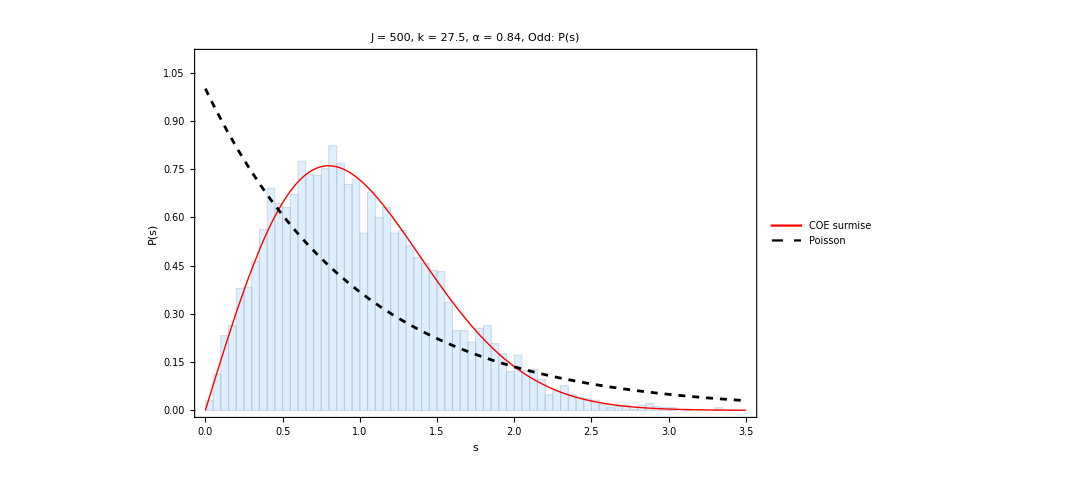

Even_cumulative_s

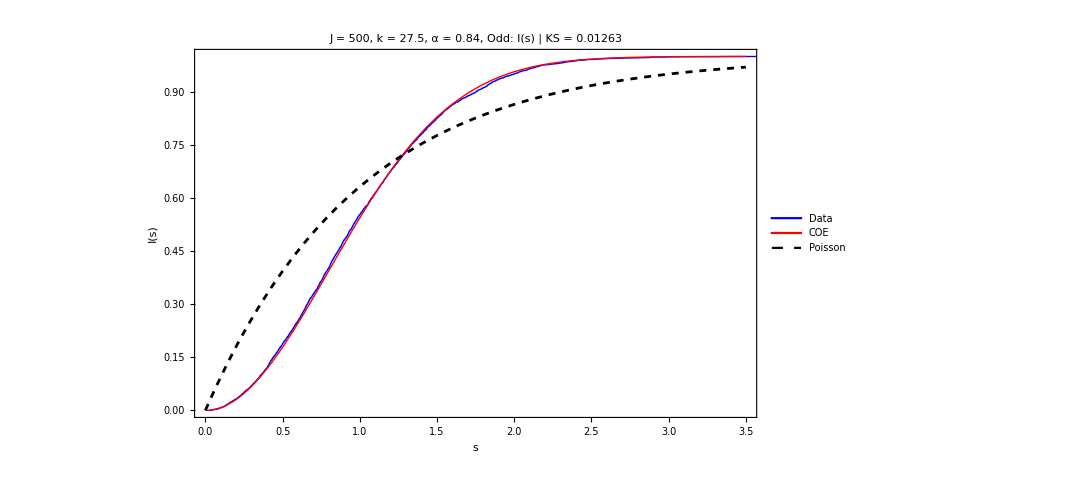

Even_pr

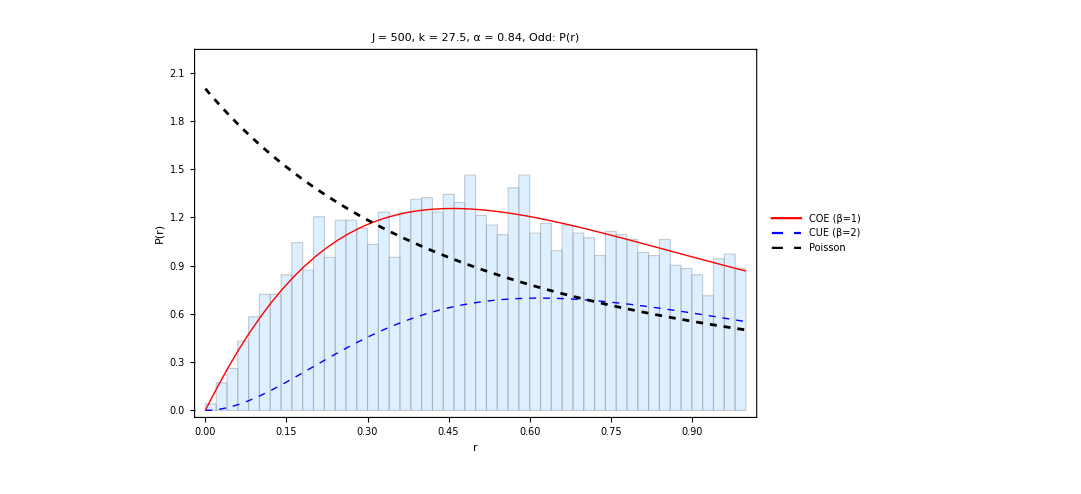

Even_cumulative_r

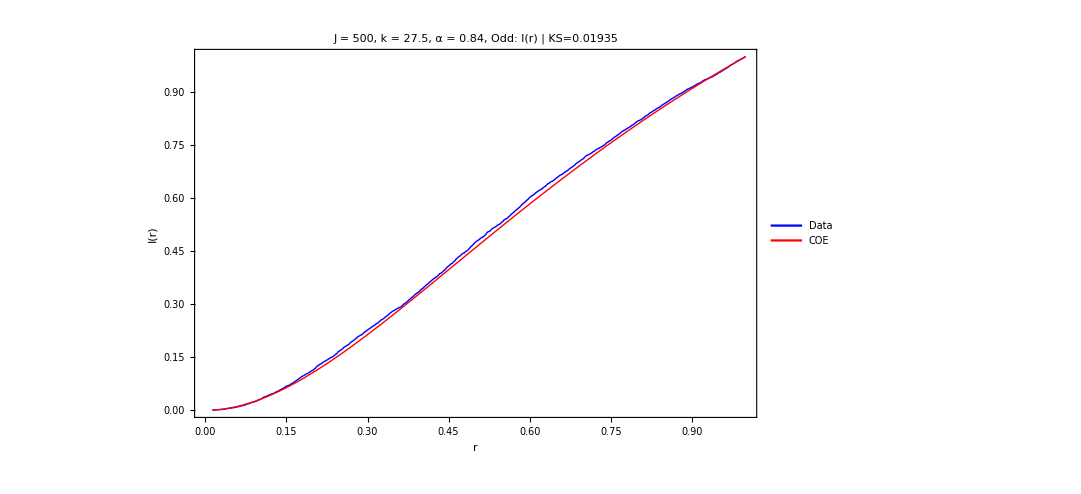

--- Odd ---

<s>=1., Var(s)=0.28772  (COE: 0.2732)

<r>=0.5293  (COE: 0.5359)

Odd_nnsd

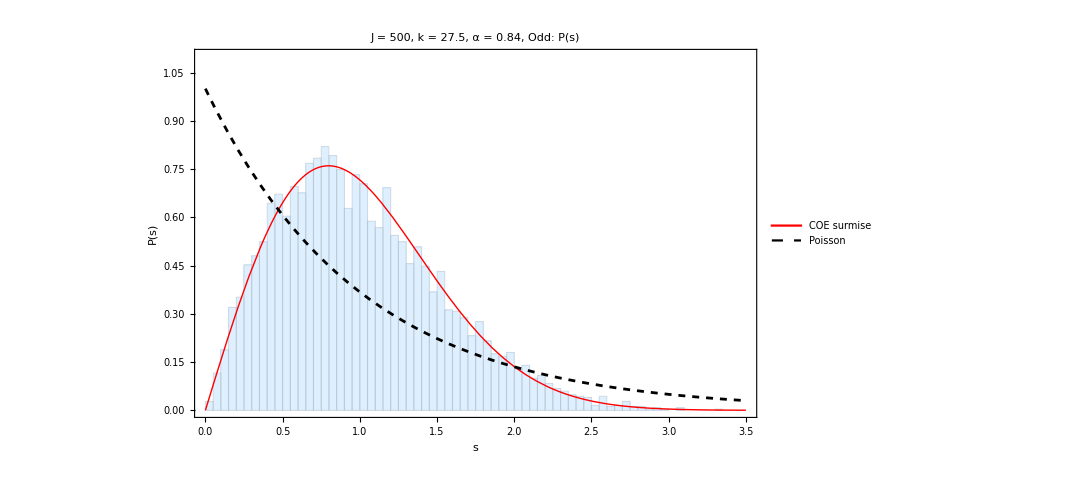

Odd_cumulative_s

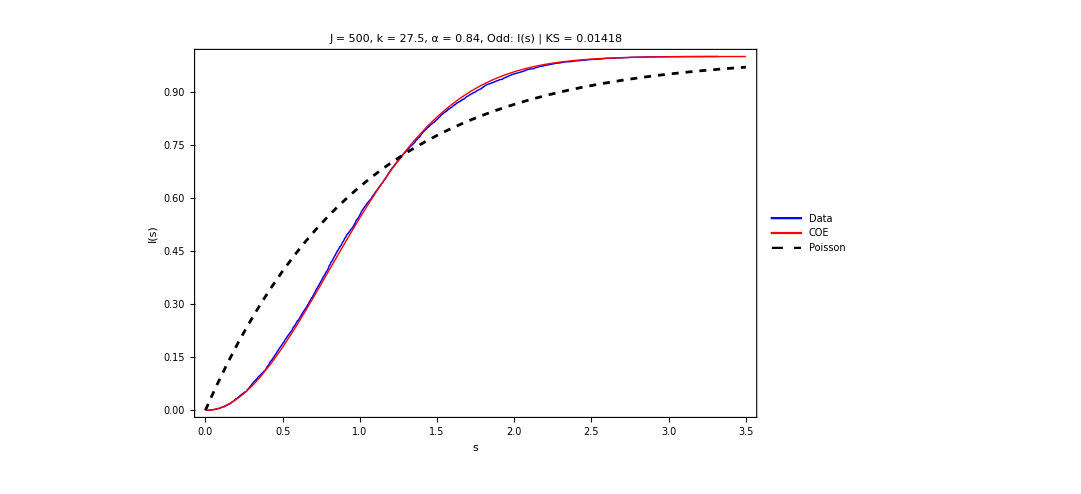

Odd_pr

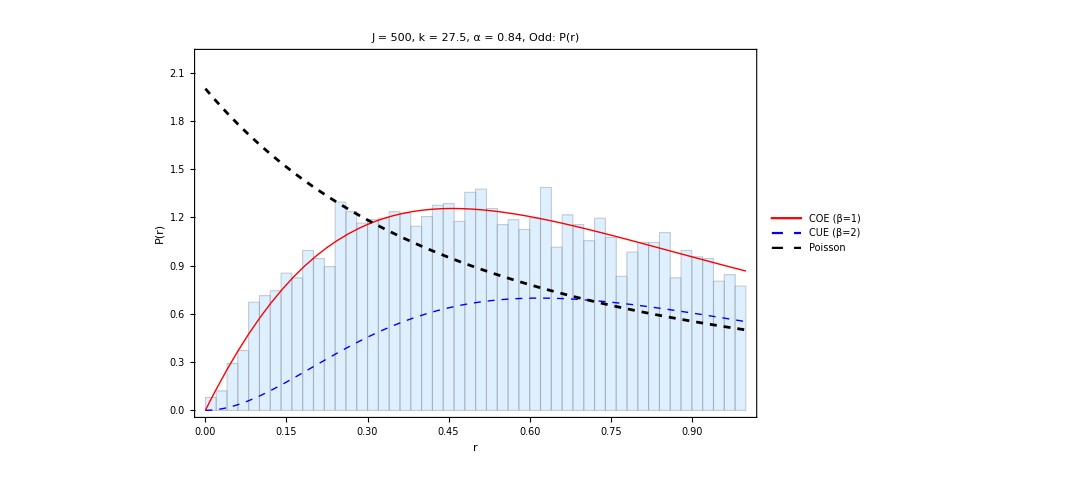

Odd_cumulative_r

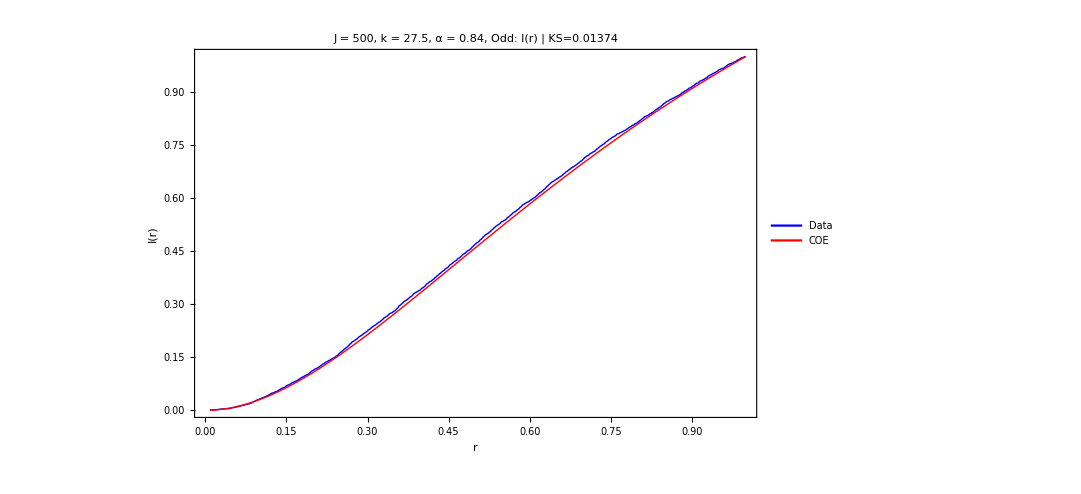

```mathematica
(* ================================================================ *)
(* MODULE 6: NNSD + P(r)                                            *)
(* ================================================================ *)

Print["\n=== SPACING STATISTICS ==="];
Do[
specList = qktEnsemble[sec];
  spacings = PoolSpacings[specList];
  ratios   = PoolSpacingRatios[specList];

  Print["--- ", sec, " ---"];
  Print["  <s>=", NumberForm[Mean[spacings], 5],
    ", Var(s)=", NumberForm[Variance[spacings], 5],
    "  (COE: ", NumberForm[N[4/Pi - 1], 4], ")"];
  Print["  <r>=", NumberForm[Mean[ratios], 5],
    "  (COE: 0.5359)"];

  SavePlot[PlotNNSD[spacings, mainLabel], sec <> "_nnsd"];
  SavePlot[PlotCumulativeS[spacings, mainLabel], sec <> "_cumulative_s"];
  SavePlot[PlotPrHist[ratios, mainLabel], sec <> "_pr"];
  SavePlot[PlotCumulativeR[ratios, mainLabel], sec <> "_cumulative_r"];

  Export[FileNameJoin[{If[sec == "Even", evenDir, oddDir],
    "spacings.wdx"}], spacings, "WDX"];
  Export[FileNameJoin[{If[sec == "Even", evenDir, oddDir],
    "ratios.wdx"}], ratios, "WDX"];
, {sec, {"Even", "Odd"}}];
```

## I(s)-I

```mathematica
qktEnsemble//Dimensions
```

{2}

```mathematica
qktEnsemble["Odd"]//Dimensions
```

{10}

```mathematica
qktEnsemble[["Odd"]][[1,2]];
```

```mathematica
(*1. Assume'eigenvalues' is your list of complex eigenvalues from the Floquet operator*)(*Extract the phases (quasienergies) and sort them*)
phases=qktEnsemble[["Odd"]][[1,2]];
Nlevels=Length[phases];

(*2. Compute the nearest-neighbor spacings with periodic boundary conditions*)
(*Since phases are in (-Pi,Pi],the total length of the spectrum is 2*Pi*)
rawSpacings=Differences[phases];
AppendTo[rawSpacings,(2 Pi-Last[phases])+First[phases]];

(*3. Unfold the spectrum*)
(*For Floquet operators,the density of states is uniform,so the mean spacing is just 2*Pi/N*)
meanSpacing=2 Pi/Nlevels;
sVals=rawSpacings/meanSpacing;

(*4. Compute the adjacent gap ratios (r)*)
(*We use the bounded definition:r_i=Min[s_i,s_{i+1}]/Max[s_i,s_{i+1}]*)
rVals=Table[Min[sVals[[i]],sVals[[Mod[i,Nlevels]+1]]]/Max[sVals[[i]],sVals[[Mod[i,Nlevels]+1]]],{i,1,Nlevels}];
```

```mathematica
(*5. Create the Experimental (Numerical) Cumulative Distributions*)
(*EmpiricalDistribution creates a step function from the data*)
distS=EmpiricalDistribution[sVals];
distR=EmpiricalDistribution[rVals];

expCDFS[x_]:=CDF[distS,x];
expCDFR[x_]:=CDF[distR,x];

(*6. Define the Theoretical Distributions (COE/GOE,beta=1)*)
(*Wigner surmise for spacing s*)
theoCDFS[x_]:=1-Exp[-(Pi/4)*x^2];

(*Atas et al.distribution for the bounded gap ratio r*)
theoPDFR[x_]:=2*(27/8)*(x+x^2)/(1+x+x^2)^(5/2);
(*Mathematica can integrate this analytically for the CDF*)
theoCDFR[x_]=Integrate[theoPDFR[r],{r,0,x}];
```

```mathematica
(*7. Plot and Compare the Integrated Distributions*)
plotS=Plot[{expCDFS[x],theoCDFS[x]},{x,0,4},PlotStyle->{{Black,Thick},{Red,Dashed}},PlotLegends->{"Experimental I(s)","Wigner I(s)"},Frame->True,FrameLabel->{"Normalized Spacing s","Cumulative Probability I(s)"},FrameStyle->Directive[Black,20],PlotLabel->"Integrated Nearest-Neighbor Spacing",ImageSize->800];

plotR=Plot[{expCDFR[x],theoCDFR[x]},{x,0,1},PlotStyle->{{Black,Thick},{Red,Dashed}},PlotLegends->{"Experimental I(r)","GOE/COE I(r)"},Frame->True,FrameLabel->{"Gap Ratio r","Cumulative Probability I(r)"},FrameStyle->Directive[Black,20],PlotLabel->"Integrated Adjacent Gap Ratio",ImageSize->800];
```

```mathematica
plotS
plotR
```

## Measuring deviations

```mathematica
(*1. Define the theoretical Probability Density Function (PDF) for Wigner*)
theoPDFS[x_]:=(Pi/2)*x*Exp[-(Pi/4)*x^2];

(*2. Define the two squared difference functions*)
(*Raw squared difference (MSD integrand)*)
msdDiff[x_]:=(expCDFS[x]-theoCDFS[x])^2;
(*Weighted squared difference (CvM integrand)*)
cvmDiff[x_]:=(expCDFS[x]-theoCDFS[x])^2*theoPDFS[x];
```

```mathematica
(*3. Plot the Raw MSD Difference*)
plotMSD=Plot[msdDiff[x],{x,0,4},PlotStyle->{Blue,Thick},PlotRange->All,Frame->True,FrameLabel->{"Normalized Spacing s","\!\(\*SuperscriptBox[\(Δ\), \(2\)]\)(s)"},PlotLabel->"Raw MSD Integrand\n(Unweighted Error)",GridLines->Automatic,FrameStyle->Directive[Black,20],LabelStyle->Directive[Black,20],ImageSize->800]
```

```mathematica
(*4. Plot the CvM Weighted Difference*)
plotCvM=Plot[cvmDiff[x],{x,0,4},PlotStyle->{Darker[Green],Thick},PlotRange->All,Frame->True,FrameLabel->{"Normalized Spacing s","\!\(\*SuperscriptBox[\(Δ\), \(2\)]\)(s) × P(s)"},PlotLabel->"CvM Integrand\n(Weighted Error)",GridLines->Automatic,FrameStyle->Directive[Black,20],LabelStyle->Directive[Black,20],ImageSize->800]
```

```mathematica
(*1. Define the upper limit as before*)
maxIntegrationLimit=Max[sVals]+2;
(*2. Create a very dense grid of points to evaluate (e.g.,step size of 0.001)*)
dx=0.001;
gridS=Range[0,maxIntegrationLimit,dx];
(*3. Calculate the total deviations using a fast discrete sum*)
totalMSD=Total[msdDiff/@gridS]*dx;
totalCvM=Total[cvmDiff/@gridS]*dx;
(*Format the numbers to scientific notation for clean display*)
textMSD="Total MSD: "<>ToString[ScientificForm[totalMSD,3]];
textCvM="Total CvM: "<>ToString[ScientificForm[totalCvM,3]];
```

```mathematica
totalMSD
totalCvM
```

0.000561955

0.000264892

```mathematica
(*Format the numbers to scientific notation or 4 decimal places for clean display*)
textMSD="Total MSD: "<>ToString[ScientificForm[totalMSD,3]];
textCvM="Total CvM: "<>ToString[ScientificForm[totalCvM,3]];
```

```mathematica
(*2. Plot the Raw MSD Difference with the total value inset*)
plotMSD=Plot[msdDiff[x],{x,0,4},PlotStyle->{Blue,Thick},PlotRange->All,Frame->True,FrameLabel->{"Normalized Spacing s","\!\(\*SuperscriptBox[\(Δ\), \(2\)]\)(s)"},PlotLabel->"Raw MSD Integrand\n(Unweighted Error)",GridLines->Automatic,FrameStyle->Directive[Black,20],LabelStyle->Directive[Black,20],ImageSize->800,Epilog->Inset[Framed[Style[textMSD,12,Bold,Black],Background->White,RoundingRadius->3],Scaled[{0.95,0.95}],{Right,Top}]]
```

# Test

```mathematica
(* ================================================================ *)
(* MODULE 1: GLOBAL PARAMETERS                                     *)
(* ================================================================ *)

J       = 500;
alpha   = 0.84;
kCenter = 27.5;
delta   = 0.01;
nQKT    = 10;
```

```mathematica
(* ================================================================ *)
(* MODULE 4: QKT ENSEMBLE                                          *)
(* ================================================================ *)

(*Instead of using RandomReal to generate a list,hardcode it as a single value list*)
kList=RandomReal[{kCenter-delta,kCenter+delta},nQKT];
Print["\nDiagonalizing single QKT matrix (J=",J,", k=",kCenter,")..."];
AbsoluteTiming[qktEnsemble=GenerateQKTEnsemble[J,alpha,kList];]
Print["Even N = ",qktEnsemble["Even"][[1]]["N"],", Odd N = ",qktEnsemble["Odd"][[1]]["N"]];

dimE = qktEnsemble["Even"][[1]]["N"];
dimO = qktEnsemble["Odd"][[1]]["N"];
Print["  Even N = ", dimE, ", Odd N = ", dimO];

(* --- Export spectra --- *)
Export[FileNameJoin[{evenDir, "spectra.wdx"}], qktEnsemble["Even"], "WDX"];
Export[FileNameJoin[{oddDir, "spectra.wdx"}], qktEnsemble["Odd"], "WDX"];
Print["  Spectra exported"];
```

Diagonalizing single QKT matrix (J=500, k=27.5)...

{29.0775,Null}

Even N = 501, Odd N = 500

Even N = 501, Odd N = 500

Spectra exported

```mathematica
(* ==========================================*)(*1. DATA EXTRACTION AND UNFOLDING*)(* ==========================================*)
phases=qktEnsemble[["Odd"]][[1,2]];
Nlevels=Length[phases];
rawSpacings=Differences[phases];
AppendTo[rawSpacings,(2 Pi-Last[phases])+First[phases]];
meanSpacing=2 Pi/Nlevels;
sVals=rawSpacings/meanSpacing;
rVals=Table[Min[sVals[[i]],sVals[[Mod[i,Nlevels]+1]]]/Max[sVals[[i]],sVals[[Mod[i,Nlevels]+1]]],{i,1,Nlevels}];
```

```mathematica
(* ==========================================*)
(*2. DEFINE EMPIRICAL AND THEORETICAL CURVES*)
(* ==========================================*)
distS=EmpiricalDistribution[sVals];
distR=EmpiricalDistribution[rVals];

expCDFS[x_]:=CDF[distS,x];
expCDFR[x_]:=CDF[distR,x];

(*Theoretical P(s) and I(s)[Wigner/GOE]*)
theoPDFS[x_]:=(Pi/2)*x*Exp[-(Pi/4)*x^2];
theoCDFS[x_]:=1-Exp[-(Pi/4)*x^2];

(*Atas et al.distribution for the bounded gap ratio r*)
theoPDFR[x_]:=2*(27/8)*(x+x^2)/(1+x+x^2)^(5/2);

(*Add Assumptions to prevent ConditionalExpression outputs*)
theoCDFR[x_]=Simplify[Integrate[theoPDFR[r],{r,0,x}],Assumptions->x>0];

msdDiffS[x_]:=(expCDFS[x]-theoCDFS[x])^2;
cvmDiffS[x_]:=(expCDFS[x]-theoCDFS[x])^2*theoPDFS[x];

msdDiffR[x_]:=(expCDFR[x]-theoCDFR[x])^2;
cvmDiffR[x_]:=(expCDFR[x]-theoCDFR[x])^2*theoPDFR[x];
```

```mathematica
(* ==========================================*)(*3. DEFINE ERROR INTEGRANDS& COMPUTE AREAS*)(* ==========================================*)
dx=0.001;
maxLimitS=Max[sVals]+2;

(*START THE GRIDS AT dx INSTEAD OF 0 TO AVOID 1/0 ERRORS*)
gridS=Range[dx,maxLimitS,dx];
gridR=Range[dx,1,dx];

totalMSDS=Total[msdDiffS/@gridS]*dx;
totalCvMS=Total[cvmDiffS/@gridS]*dx;
totalMSDR=Total[msdDiffR/@gridR]*dx;
totalCvMR=Total[cvmDiffR/@gridR]*dx;

(*Format the numbers*)
textMSDS="Total: "<>ToString[ScientificForm[totalMSDS,3]];
textCvMS="Total: "<>ToString[ScientificForm[totalCvMS,3]];
textMSDR="Total: "<>ToString[ScientificForm[totalMSDR,3]];
textCvMR="Total: "<>ToString[ScientificForm[totalCvMR,3]];
```

```mathematica
(* ==========================================*)
(*4. ROW 1:P(s) and P(r)[PDFs]*)
(* ==========================================*)
plotPDFS=Show[Histogram[sVals,Automatic,"PDF",ChartStyle->Directive[LightGray,EdgeForm[Gray]]],Plot[theoPDFS[x],{x,0,4},PlotStyle->{Red,Dashed,Thick}],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"Spacing s","P(s)"},PlotLabel->"Probability Density P(s)",LabelStyle->Directive[Black,25]];

plotPDFR=Show[Histogram[rVals,Automatic,"PDF",ChartStyle->Directive[LightGray,EdgeForm[Gray]]],Plot[theoPDFR[x],{x,0,1},PlotStyle->{Red,Dashed,Thick}],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"Gap Ratio r","P(r)"},PlotLabel->"Probability Density P(r)",LabelStyle->Directive[Black,25]];

(* ==========================================*)
(*5. ROW 2:I(s) and I(r)[CDFs]*)
(* ==========================================*)
plotCDFS=Plot[{expCDFS[x],theoCDFS[x]},{x,0,4},PlotStyle->{{Black,Thick},{Red,Dashed}},Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"Spacing s","I(s)"},PlotLabel->"Cumulative Distribution I(s)",PlotLegends->Placed[{"Exp","GOE"},{Right,Bottom}],LabelStyle->Directive[Black,25]];

plotCDFR=Plot[{expCDFR[x],theoCDFR[x]},{x,0,1},PlotStyle->{{Black,Thick},{Red,Dashed}},Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"Gap Ratio r","I(r)"},PlotLabel->"Cumulative Distribution I(r)",PlotLegends->Placed[{"Exp","GOE"},{Right,Bottom}],LabelStyle->Directive[Black,25]];

(* ==========================================*)
(*6. ROW 3:Raw MSD Integrands*)
(* ==========================================*)
plotMSDS=Plot[msdDiffS[x],{x,0,4},PlotStyle->{Blue,Thick},PlotRange->All,Frame->True,FrameStyle->Directive[Black,20],GridLines->Automatic,FrameLabel->{"Spacing s","\!\(\*SuperscriptBox[\(Δ\), \(2\)]\)(s)"},PlotLabel->"Raw MSD Integrand (s)",Epilog->Inset[Framed[Style[textMSDS,11,Bold,Black],Background->White],Scaled[{0.95,0.95}],{Right,Top}],LabelStyle->Directive[Black,25]];

plotMSDR=Plot[msdDiffR[x],{x,0,1},PlotStyle->{Blue,Thick},PlotRange->All,Frame->True,FrameStyle->Directive[Black,20],GridLines->Automatic,FrameLabel->{"Gap Ratio r","\!\(\*SuperscriptBox[\(Δ\), \(2\)]\)(r)"},PlotLabel->"Raw MSD Integrand (r)",Epilog->Inset[Framed[Style[textMSDR,11,Bold,Black],Background->White],Scaled[{0.95,0.95}],{Right,Top}],LabelStyle->Directive[Black,25]];

(* ==========================================*)
(*7. ROW 4:CvM Weighted Integrands*)
(* ==========================================*)
plotCvMS=Plot[cvmDiffS[x],{x,0,4},PlotStyle->{Darker[Green],Thick},PlotRange->All,Frame->True,FrameStyle->Directive[Black,20],GridLines->Automatic,FrameLabel->{"Spacing s","\!\(\*SuperscriptBox[\(Δ\), \(2\)]\)(s) × P(s)"},PlotLabel->"CvM Integrand (s)",Epilog->Inset[Framed[Style[textCvMS,11,Bold,Black],Background->White],Scaled[{0.95,0.95}],{Right,Top}],LabelStyle->Directive[Black,25]];

plotCvMR=Plot[cvmDiffR[x],{x,0,1},PlotStyle->{Darker[Green],Thick},PlotRange->All,Frame->True,FrameStyle->Directive[Black,20],GridLines->Automatic,FrameLabel->{"Gap Ratio r","\!\(\*SuperscriptBox[\(Δ\), \(2\)]\)(r) × P(r)"},PlotLabel->"CvM Integrand (r)",Epilog->Inset[Framed[Style[textCvMR,11,Bold,Black],Background->White],Scaled[{0.95,0.95}],{Right,Top}],LabelStyle->Directive[Black,25]];
```

```mathematica
(* ==========================================*)
(*8. ASSEMBLE THE COLLAGE*)
(* ==========================================*)
testplot=GraphicsGrid[{{plotPDFS,plotPDFR},{plotCDFS,plotCDFR},{plotMSDS,plotMSDR},{plotCvMS,plotCvMR}},Spacings->{30,30}];
```

```mathematica
Export["testplot.png",testplot,ImageResolution->200,ImageSize->1200]
```

testplot.png

# Test 2

```mathematica
dataeven=Import["C:\\Users\\Miguel\\Desktop\\plots_J_500\\evenspectra_k27.5.mx"];
dataodd=Import["C:\\Users\\Miguel\\Desktop\\plots_J_500\\oddspectra_k27.5.mx"];
```

```mathematica
dataeven=Import["C:\\Users\\Miguel\\Desktop\\plots_J_1000\\spectra_k25.0_even.mx"];
dataodd=Import["C:\\Users\\Miguel\\Desktop\\plots_J_1000\\spectra_k25.0.mx"];
```

```mathematica
dataeven=Import["C:\\Users\\Miguel\\Desktop\\plots_J_1500\\evenspectra_k19.5.mx"];
dataodd=Import["C:\\Users\\Miguel\\Desktop\\plots_J_1500\\oddspectra_k19.5.mx"];
```

```mathematica
qktEnsemble=<|"Even"->dataeven,"Odd"->dataodd|>;
```

```mathematica
collageDir=FileNameJoin[{resultsDir,"individual"}];
EnsureDir[collageDir];
```

```mathematica
nReal = Length[qktEnsemble["Even"]];
```

```mathematica
(* ================================================================ *)
(* EXECUTION: INDIVIDUAL REALIZATIONS                               *)
(* ================================================================ *)

Print["=== INDIVIDUAL COLLAGES ==="];

Do[
  Module[{stE, stO, flE, flO, colE, colO, collage},
    stE = ExtractSpacingsAndRatios[qktEnsemble["Even"][[i]]];
    stO = ExtractSpacingsAndRatios[qktEnsemble["Odd"][[i]]];
    flE = GetFluctuationsCentered[qktEnsemble["Even"][[i]]];
    flO = GetFluctuationsCentered[qktEnsemble["Odd"][[i]]];

    colE = MakeRowPlots[stE["SortedS"], stE["SortedR"], flE, "Even"];
    colO = MakeRowPlots[stO["SortedS"], stO["SortedR"], flO, "Odd"];

    collage = Grid[
      Prepend[
        Transpose[{colE, colO}],
        {Style["Even", Bold, 20], Style["Odd", Bold, 20]}
      ],
      Spacings -> {1, 0.5},
      Frame -> All, FrameStyle -> GrayLevel[0.85]
    ];

    Export[
      FileNameJoin[{collageDir,
        "realization_" <> StringPadLeft[ToString[i], 4, "0"] <> ".png"}],
      Rasterize[collage, ImageResolution -> 150, Background -> White]
    ];

    If[Mod[i, 50] == 0 || i == 1,
      Print["  Exported realization ", i, "/", nReal]];
  ];
, {i, 2}];

Print["Individual collages complete: ", collageDir];
```

=== INDIVIDUAL COLLAGES ===

Exported realization 1/500

Individual collages complete: C:\Users\Miguel\Github\Chaotic_eigenfunctions\Spectral measures analysis\Results\J500_k27.5\individual

## Ensemble

```mathematica
(* ================================================================ *)
(* EXECUTION: ENSEMBLE-POOLED COLLAGE                               *)
(* ================================================================ *)

Print["\n=== ENSEMBLE COLLAGE ==="];

Module[{spE, spO, rE, rO, flE, flO, colE, colO, ensCollage},
  spE = Sort[Flatten[Map[NNSpacings, qktEnsemble["Even"]]]];
  spO = Sort[Flatten[Map[NNSpacings, qktEnsemble["Odd"]]]];
  rE  = Sort[PoolSpacingRatios[qktEnsemble["Even"]]];
  rO  = Sort[PoolSpacingRatios[qktEnsemble["Odd"]]];

  Print["  Even: <s>=", NumberForm[Mean[spE], 5],
    ", <r>=", NumberForm[Mean[rE], 5]];
  Print["  Odd:  <s>=", NumberForm[Mean[spO], 5],
    ", <r>=", NumberForm[Mean[rO], 5]];

  flE = GetFluctuationsCentered[qktEnsemble["Even"][[1]]];
  flO = GetFluctuationsCentered[qktEnsemble["Odd"][[1]]];

  colE = MakeRowPlots[spE, rE, flE, "Even (ensemble)"];
  colO = MakeRowPlots[spO, rO, flO, "Odd (ensemble)"];

  ensCollage = Grid[
    Prepend[
      Transpose[{colE, colO}],
      {Style["Even (pooled " <> ToString[nReal] <> ")", Bold, 20],
       Style["Odd (pooled " <> ToString[nReal] <> ")", Bold, 20]}
    ],
    Spacings -> {1, 0.5},
    Frame -> All, FrameStyle -> GrayLevel[0.85]
  ];

  Export[
    FileNameJoin[{plotDir, "ensemble_collage.png"}],
    Rasterize[ensCollage, ImageResolution -> 150, Background -> White]
  ];
  Print["  Ensemble collage exported"];
];
```

=== ENSEMBLE COLLAGE ===

Even: <s>=1., <r>=0.52868

Odd:  <s>=1., <r>=0.53409

Ensemble collage exported

# Test 3

```mathematica
(* ================================================================ *)
(* EXECUTION: PER-REALIZATION ERRORS (PARALLELIZED)                 *)
(* ================================================================ *)

Print["\n=== PER-REALIZATION GoF (parallel) ==="];

DistributeDefinitions[
  ComputeGoFSingle, NNSpacings, IntWignerCOE, IntPrCOEFast,
  KSFromSorted, CvMFromSorted, MSDFromSorted];

(* Even sector *)
Print["  Computing Even sector..."];
{tE, gofEvenAll} = AbsoluteTiming[
  ParallelTable[
    ComputeGoFSingle[qktEnsemble["Even"][[i]]],
    {i, nReal}, Method -> "CoarsestGrained"
  ]
];
Print["  Even done in ", Round[tE, 0.1], "s"];

(* Odd sector *)
Print["  Computing Odd sector..."];
{tO, gofOddAll} = AbsoluteTiming[
  ParallelTable[
    ComputeGoFSingle[qktEnsemble["Odd"][[i]]],
    {i, nReal}, Method -> "CoarsestGrained"
  ]
];
Print["  Odd done in ", Round[tO, 0.1], "s"];

(* Unpack into named columns *)
(* Each row: {KS_s, CvM_s, MSD_s, KS_r, CvM_r, MSD_r} *)
gofEvenTable = Association[
  "KS_s"  -> gofEvenAll[[All, 1]],
  "CvM_s" -> gofEvenAll[[All, 2]],
  "MSD_s" -> gofEvenAll[[All, 3]],
  "KS_r"  -> gofEvenAll[[All, 4]],
  "CvM_r" -> gofEvenAll[[All, 5]],
  "MSD_r" -> gofEvenAll[[All, 6]]
];

gofOddTable = Association[
  "KS_s"  -> gofOddAll[[All, 1]],
  "CvM_s" -> gofOddAll[[All, 2]],
  "MSD_s" -> gofOddAll[[All, 3]],
  "KS_r"  -> gofOddAll[[All, 4]],
  "CvM_r" -> gofOddAll[[All, 5]],
  "MSD_r" -> gofOddAll[[All, 6]]
];

(* Print summary statistics *)
Print["\n--- Even sector (per-realization) ---"];
Do[
  Print["  ", metric, ":  mean=",
    NumberForm[Mean[gofEvenTable[metric]], 4],
    "  std=", NumberForm[StandardDeviation[gofEvenTable[metric]], 4],
    "  max=", NumberForm[Max[gofEvenTable[metric]], 4]];
, {metric, {"KS_s", "CvM_s", "MSD_s", "KS_r", "CvM_r", "MSD_r"}}];

Print["\n--- Odd sector (per-realization) ---"];
Do[
  Print["  ", metric, ":  mean=",
    NumberForm[Mean[gofOddTable[metric]], 4],
    "  std=", NumberForm[StandardDeviation[gofOddTable[metric]], 4],
    "  max=", NumberForm[Max[gofOddTable[metric]], 4]];
, {metric, {"KS_s", "CvM_s", "MSD_s", "KS_r", "CvM_r", "MSD_r"}}];

(* Export per-realization data *)
Export[FileNameJoin[{evenDir, "gof_per_realization.wdx"}], gofEvenTable, "WDX"];
Export[FileNameJoin[{oddDir, "gof_per_realization.wdx"}], gofOddTable, "WDX"];
Print["\nPer-realization GoF exported"];
```

=== PER-REALIZATION GoF (parallel) ===

Computing Even sector...

Even done in 1.3s

Computing Odd sector...

Odd done in 0.4s

--- Even sector (per-realization) ---

KS_s:  mean=0.03457  std=0.01351  max=0.06018

CvM_s:  mean=0.0004608  std=0.0002319  max=0.000856

MSD_s:  mean=0.0003052  std=0.0002402  max=0.0007118

KS_r:  mean=0.04905  std=0.01755  max=0.08451

CvM_r:  mean=0.0008676  std=0.000548  max=0.00218

MSD_r:  mean=0.0007263  std=0.0005728  max=0.002086

--- Odd sector (per-realization) ---

KS_s:  mean=0.04138  std=0.01045  max=0.0637

CvM_s:  mean=0.0004507  std=0.000143  max=0.0007034

MSD_s:  mean=0.0002927  std=0.0001494  max=0.0005537

KS_r:  mean=0.0379  std=0.009276  max=0.05686

CvM_r:  mean=0.0004959  std=0.0002039  max=0.0008514

MSD_r:  mean=0.00035  std=0.0002176  max=0.0007305

Per-realization GoF exported

```mathematica
(* ================================================================ *)
(* EXECUTION: ENSEMBLE-POOLED ERRORS                                *)
(* ================================================================ *)

Print["\n=== ENSEMBLE-POOLED GoF ==="];

{tEE, gofEvenEns} = AbsoluteTiming[
  ComputeGoFEnsemble[qktEnsemble["Even"]]];
{tOE, gofOddEns} = AbsoluteTiming[
  ComputeGoFEnsemble[qktEnsemble["Odd"]]];

Print["\n--- Even ensemble ---"];
Do[Print["  ", k, " = ", NumberForm[gofEvenEns[k], 5]],
  {k, {"KS_s", "CvM_s", "MSD_s", "KS_r", "CvM_r", "MSD_r"}}];

Print["\n--- Odd ensemble ---"];
Do[Print["  ", k, " = ", NumberForm[gofOddEns[k], 5]],
  {k, {"KS_s", "CvM_s", "MSD_s", "KS_r", "CvM_r", "MSD_r"}}];

Export[FileNameJoin[{evenDir, "gof_ensemble.wdx"}], gofEvenEns, "WDX"];
Export[FileNameJoin[{oddDir, "gof_ensemble.wdx"}], gofOddEns, "WDX"];
```

=== ENSEMBLE-POOLED GoF ===

--- Even ensemble ---

KS_s = 0.01999

CvM_s = 0.00012956

MSD_s = 0.00012925

KS_r = 0.028283

CvM_r = 0.00026549

MSD_r = 0.0002652

--- Odd ensemble ---

KS_s = 0.02977

CvM_s = 0.00017247

MSD_s = 0.00017215

KS_r = 0.019132

CvM_r = 0.00014958

MSD_r = 0.00014928

```mathematica
(* ================================================================ *)
(* VISUALIZATION: HISTOGRAMS OF PER-REALIZATION ERRORS              *)
(* ================================================================ *)

Print["\n=== GoF HISTOGRAMS ==="];

$pOpts = Sequence[ImageSize -> 800, Frame -> True,
  FrameStyle -> Directive[30, Black],
  LabelStyle -> Directive[30, Black],
  Background -> White];

Do[
  Module[{eVals, oVals, plt},
    eVals = gofEvenTable[metric];
    oVals = gofOddTable[metric];
    plt = Legended[
      Show[
        Histogram[{eVals, oVals}, Automatic, "ProbabilityDensity",
          ChartStyle -> {Directive[Blue, Opacity[0.5]],
                         Directive[Darker[Green], Opacity[0.5]]}],
        $pOpts,
        FrameLabel -> {metric, "Density"},
        PlotLabel -> metric <> " distribution across " <>
          ToString[nReal] <> " realizations"
      ],
      Placed[LineLegend[
        {Directive[Blue, Opacity[0.5]], Directive[Darker[Green], Opacity[0.5]]},
        {"Even", "Odd"},
        LabelStyle -> Directive[Black, 18]
      ], {Right, Top}]
    ];
    Export[
      FileNameJoin[{plotDir, "gof_hist_" <> metric <> ".png"}],
      Rasterize[plt, ImageResolution -> 150, Background -> White]
    ];
  ];
, {metric, {"KS_s", "CvM_s", "MSD_s", "KS_r", "CvM_r", "MSD_r"}}];

Print["GoF histograms exported"];
Print["\n=== COMPLETE ==="];
```

=== GoF HISTOGRAMS ===

GoF histograms exported

=== COMPLETE ===

# K dependence

## Results

```mathematica
klist=Range[10.,30.,0.5];
nReal=500;  (*or however many per ensemble*)

baseDirEven="C:\\Users\\Miguel\\Desktop\\plots_J_500\\spectra\\even\\";
baseDirOdd="C:\\Users\\Miguel\\Desktop\\plots_J_500\\spectra\\odd\\";

(*Format k to consistent string:10.->"10.0",10.5->"10.5"*)
kStr[k_]:=Module[{s=ToString[N[k]]},If[StringEndsQ[s,"."],s<>"0",s]];

allGofEven={};
allGofOdd={};
allratiosEven={};
allratiosOdd={};
```

```mathematica
Do[

ks=kStr[ki];
fileEven=baseDirEven<>"spectra_k"<>ks<>".mx";
fileOdd=baseDirOdd<>"spectra_k"<>ks<>".mx";
If[!FileExistsQ[fileEven]||!FileExistsQ[fileOdd],Print["  SKIP k=",ks,": file not found"];
AppendTo[allGofEven,{ki,Missing[]}];
AppendTo[allGofOdd,{ki,Missing[]}];
Continue[];];
dataeven=Import[fileEven];
dataodd=Import[fileOdd];
gofE=ParallelTable[ComputeGoFSingle[dataeven[[i]]],{i,Length[dataeven]},Method->"CoarsestGrained"];
gofO=ParallelTable[ComputeGoFSingle[dataodd[[i]]],{i,Length[dataodd]},Method->"CoarsestGrained"];

(*ratiosE=ParallelTable[MeanLevelSpacingRatio[Sort[dataeven[[i]]]],{i,Length[dataeven]},Method->"CoarsestGrained"];
ratiosO=ParallelTable[MeanLevelSpacingRatio[Sort[dataodd[[i]]]],{i,Length[dataodd]},Method->"CoarsestGrained"];*)

(*Mean over ensemble:{KS_s,CvM_s,MSD_s,KS_r,CvM_r,MSD_r}*)
AppendTo[allGofEven,{ki,Mean[gofE]}];

AppendTo[allGofOdd,{ki,Mean[gofO]}];
(*AppendTo[allratiosEven,{ki,Mean[ratiosE]}];

AppendTo[allratiosOdd,{ki,Mean[ratiosO]}];*)
Print["  k=",ks," done"];

,{ki,klist}];

(*Filter out missing entries*)
validEven=Select[allGofEven,!MissingQ[#[[2]]]&];
validOdd=Select[allGofOdd,!MissingQ[#[[2]]]&];

(*Extract:{k,metric_value} for each metric*)
kValsE=validEven[[All,1]];
kValsO=validOdd[[All,1]];
metricsE=validEven[[All,2]];  (*each is a length-6 list*)
metricsO=validOdd[[All,2]];

labels={"KS_s","CvM_s","MSD_s","KS_r","CvM_r","MSD_r"};
```

k=10.0 done

k=10.5 done

k=11.0 done

k=11.5 done

k=12.0 done

k=12.5 done

k=13.0 done

k=13.5 done

k=14.0 done

k=14.5 done

k=15.0 done

k=15.5 done

k=16.0 done

k=16.5 done

k=17.0 done

k=17.5 done

k=18.0 done

k=18.5 done

k=19.0 done

k=19.5 done

k=20.0 done

k=20.5 done

k=21.0 done

k=21.5 done

k=22.0 done

k=22.5 done

k=23.0 done

k=23.5 done

k=24.0 done

k=24.5 done

k=25.0 done

k=25.5 done

k=26.0 done

k=26.5 done

k=27.0 done

k=27.5 done

k=28.0 done

k=28.5 done

k=29.0 done

k=29.5 done

k=30.0 done

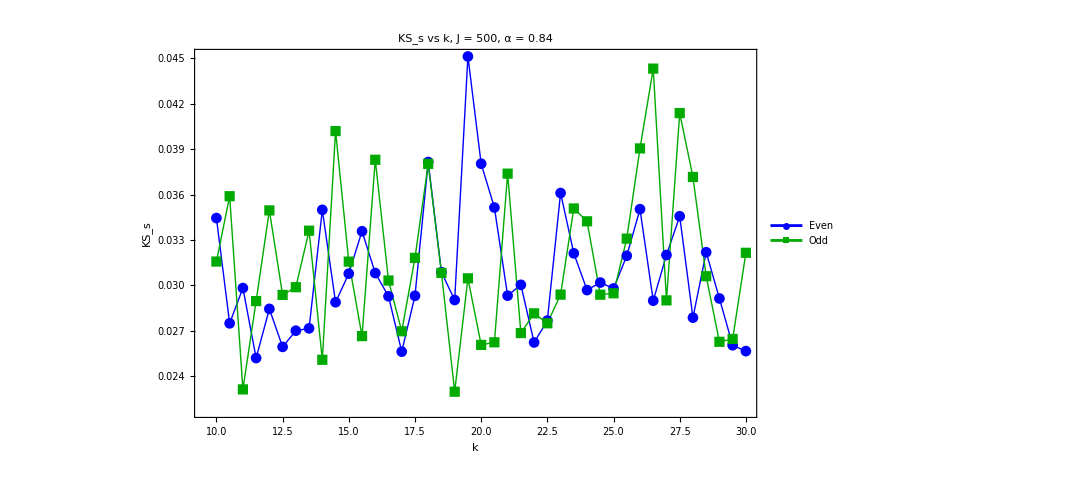

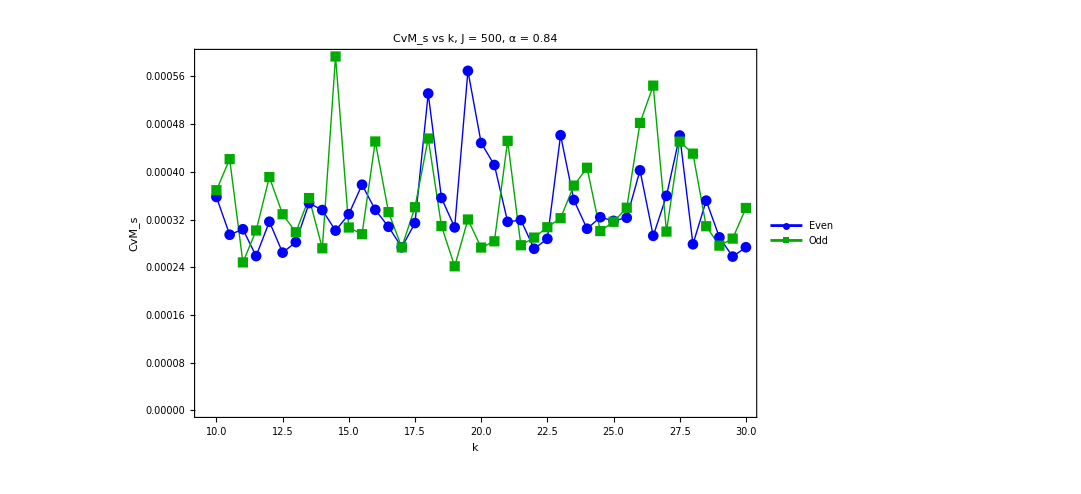

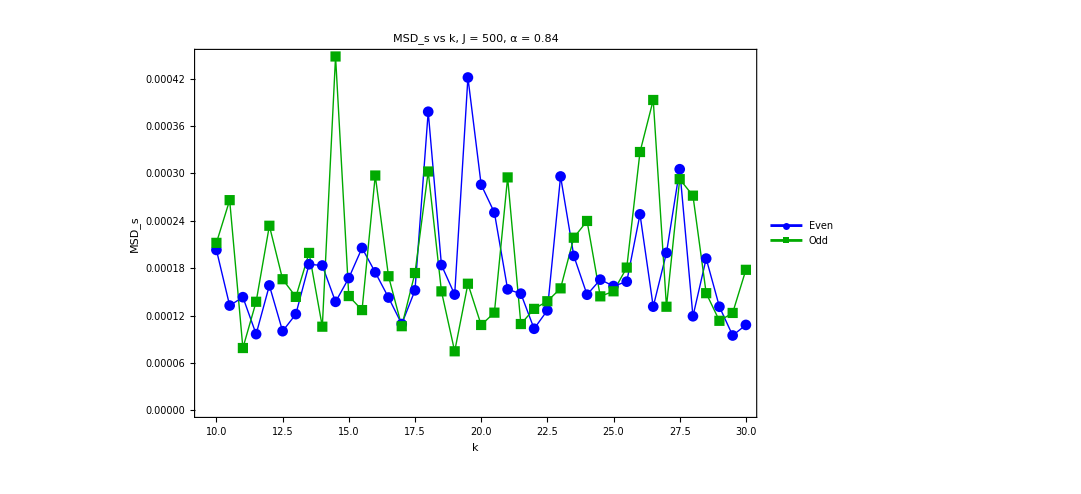

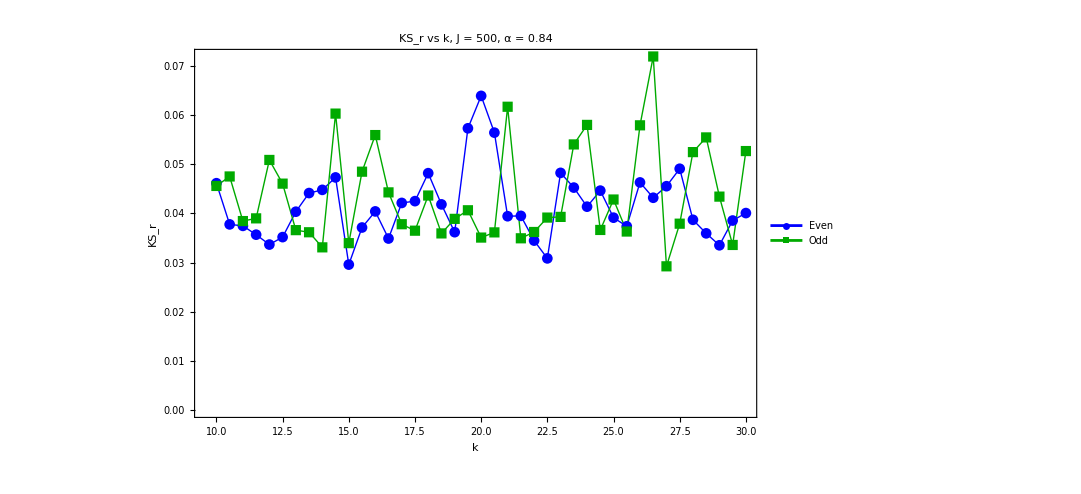

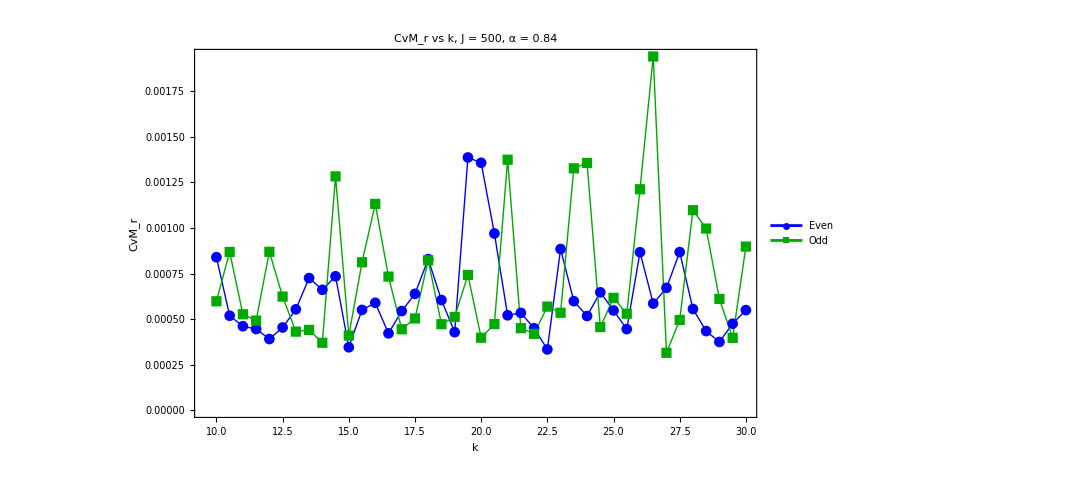

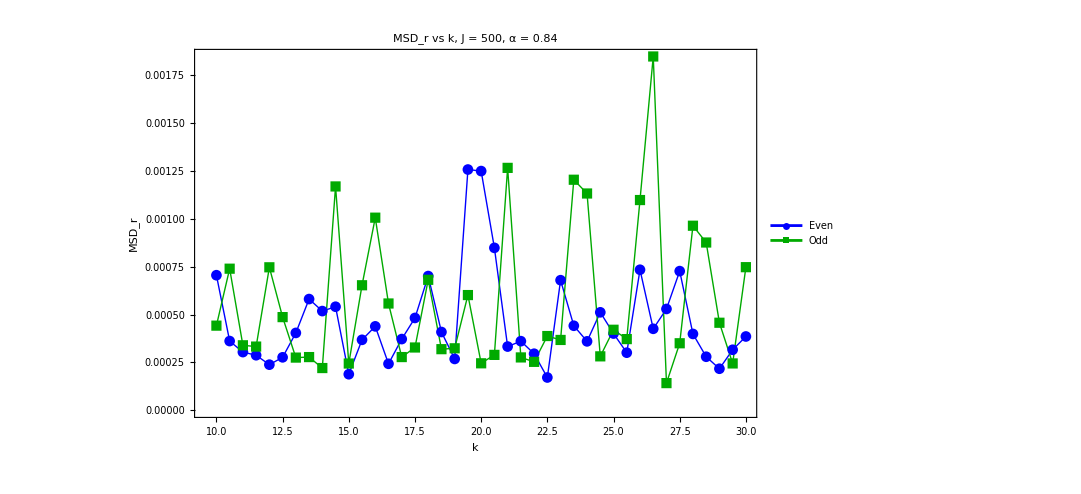

```mathematica
Do[Print[ListPlot[{Transpose[{kValsE,metricsE[[All,idx]]}],Transpose[{kValsO,metricsO[[All,idx]]}]},PlotStyle->{{Blue,Thick},{Darker[Green],Thick}},Frame->True,ImageSize->800,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black],FrameLabel->{"k",labels[[idx]]},PlotLabel->labels[[idx]]<>" vs k, J = "<>ToString[J]<>", α = 0.84",PlotLegends->Placed[{"Even","Odd"},{Right,Top}],PlotMarkers->Automatic,Joined->True,PlotRange->All]];,{idx,6}];
```